```mathematica
SetDirectory["C:\\Users\\John\\SkyDrive\\Documents\\Task\\NegPolaron"]
```

C:\Users\John\SkyDrive\Documents\Task\NegPolaron

```mathematica
Directory[]
```

D:\MMA_Scripts\Research\NegPolaron

## f1

```mathematica
egy=Import["energypf1.dat"];
```

```mathematica
Dimensions[egy]
```

{1000,200}

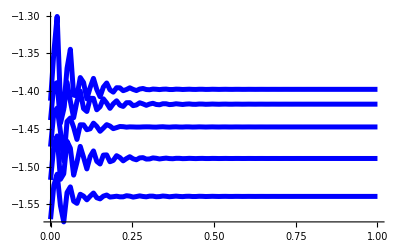

```mathematica
pf1[1]=ListPlot[(egy⟦1;;1000;;10,#1⟧&/@Range[95,99]),DataRange->{0,1},PlotRange->All,PlotStyle->Directive[Blue,Thickness[0.009]],Joined->True]
```

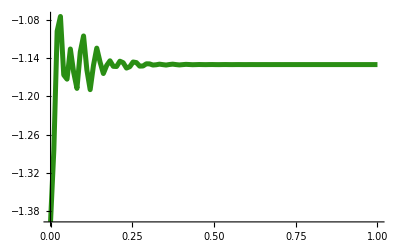

```mathematica
pf1[2]=ListPlot[egy⟦1;;1000;;10,100⟧,DataRange->{0,1},PlotRange->All,PlotStyle->Directive[ColorData["Atoms"]["Ba"],Thickness[0.009]],Joined->True]
```

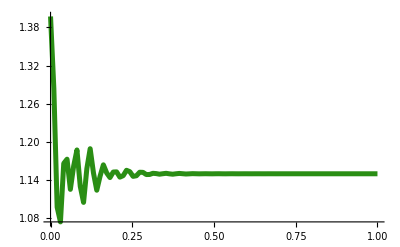

```mathematica
pf1[3]=ListPlot[egy⟦1;;1000;;10,101⟧,DataRange->{0,1},PlotRange->All,PlotStyle->Directive[ColorData["Atoms"]["Ba"],Thickness[0.009]],Joined->True]
```

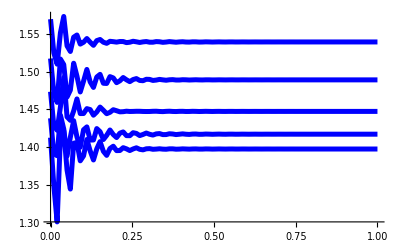

```mathematica
pf1[4]=ListPlot[(egy⟦1;;1000;;10,#1⟧&/@Range[102,106]),DataRange->{0,1},PlotRange->All,PlotStyle->Directive[Blue,Thickness[0.009]],Joined->True]
```

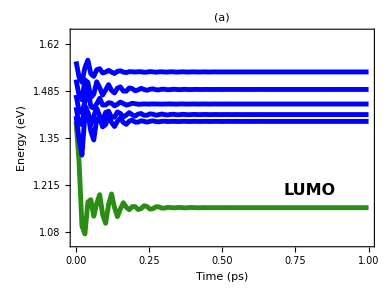

```mathematica
ff1=Show[pf1/@Range[3,4],PlotRange->{{0,1.},{1.05,1.65}},Frame->True,Axes->False,FrameStyle->Directive[Thickness[0.006],FontSize->23],FrameTicks->{{Array[#1&,5,{1.08,1.62}],None},{All,None}},FrameLabel->(Style[#1,Bold]&/@{"Time (ps)","Energy (eV)"}),ImageSize->390,AspectRatio->0.75,PlotLabel->Style["(a)",20,Bold],
Epilog->{Inset[Style["LUMO",Bold,FontSize->16],{0.8,1.2}],Inset[Style[" ",Bold,FontSize->16],{0.8,1.35}]}
]
```

```mathematica
ff1=Show[pf1/@Range[3,4],PlotRange->{{0,1.},{1.05,1.45}},Frame->True,Axes->False,FrameStyle->Directive[Thickness[0.006],FontSize->23],FrameTicks->{{Array[#1&,5,{1.08,1.42}],None},{None,None}},FrameLabel->{None,None},ImageSize->390,AspectRatio->0.75,
Epilog->{Inset[Style["LUMO",Bold,FontSize->16],{0.8,1.2}],Inset[Style["LUMO + 1",Bold,FontSize->16],{0.8,1.35}]}
]
```

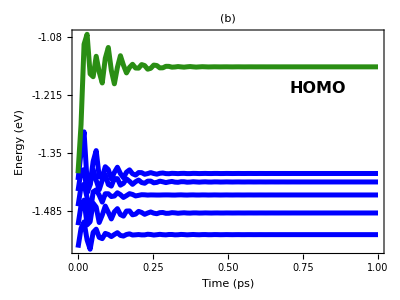

```mathematica
ff2=Show[pf1/@Range[1,2],PlotRange->{{0,1.},{-1.05,-1.65}},Frame->True,Axes->False,FrameStyle->Directive[Thickness[0.006],FontSize->23],FrameLabel->(Style[#1,Bold]&/@{"Time (ps)","Energy (eV)"}),FrameTicks->{{Array[#1&,5,{-1.08,-1.62}],None},{All,None}},ImageSize->400,AspectRatio->0.75,PlotLabel->Style["(b)",20,Bold],
Epilog->{Inset[Style["HOMO",Bold,FontSize->16],{0.8,-1.2}],Inset[Style[" ",Bold,FontSize->16],{0.8,-1.35}]}
]
```

```mathematica
ff2=Show[pf1/@Range[1,2],PlotRange->{{0,1.},{-1.05,-1.45}},Frame->True,Axes->False,FrameStyle->Directive[Thickness[0.006],FontSize->23],FrameLabel->{None,None},FrameTicks->{{Array[#1&,5,{-1.08,-1.42}],None},{None,None}},ImageSize->400,AspectRatio->0.75,PlotLabel->Style["(b)",20,Bold],
Epilog->{Inset[Style["HOMO",Bold,FontSize->16],{0.8,-1.2}],Inset[Style["HOMO + 1",Bold,FontSize->16],{0.8,-1.35}]}]
```

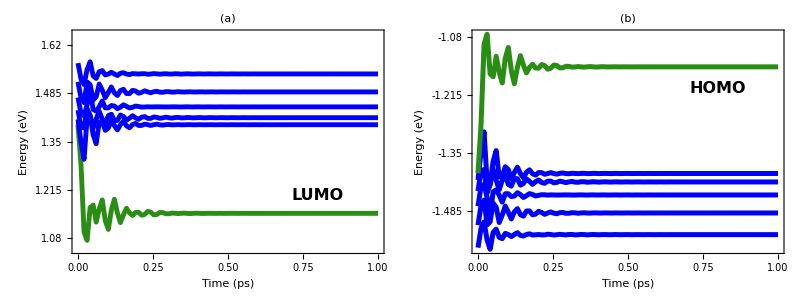

```mathematica
fo1=Grid[{{ff1,ff2}}]
```

```mathematica
Export["fo1.png",fo1,ImageResolution->600]
```

fo1.png

### Diagram

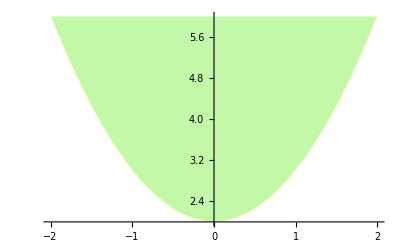

```mathematica
p1=Plot[x^2+2,{x,-2,2},Axes->True,Filling->6,FillingStyle->Directive[ColorData["Atoms"]["Cl"],Opacity[0.4]],PlotStyle->LightYellow]
```

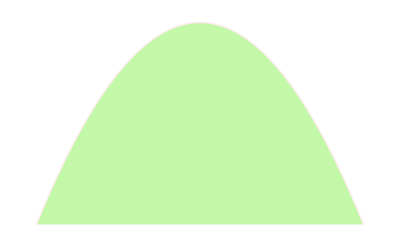

```mathematica
p2=Plot[-x^2-2,{x,-2,2},Axes->False,Filling->-6,FillingStyle->Directive[ColorData["Atoms"]["Cl"],Opacity[0.4]],PlotStyle->LightPink]
```

```mathematica
Show[p1,p2,PlotRange->All,AspectRatio->(Sqrt@5+1)/2];
```

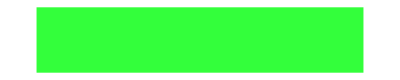

```mathematica
pr1=Graphics[{Opacity[0.8],Hue[0.34],Rectangle[{-1.5,-1},{1.5,-0.8}]}]
```

```mathematica
pr2=Graphics[{Opacity[0.8],Hue[0.34],Rectangle[{-1.5,1},{1.5,0.8}]}]
```

-Graphics-

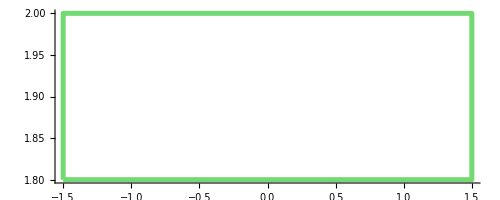

```mathematica
pr22=Graphics[{EdgeForm[Directive[Opacity[0.8],ColorData["Atoms"]["Ni"],Dashed,Thickness[0.009]]],White,Rectangle[{-1.5,1+1},{1.5,0.8+1}]},Axes->True]
```

```mathematica
{λ,sx,sy,x0,y0,len}={1./4.,3,0.2,-1.5,-1,8*sy};
pa1=Graphics[{Black,Thickness[0.02],Arrowheads[.078],Arrow[{{λ*sx+x0,y0+sy/2.-len/2.},{λ*sx+x0,y0+sy/2.+len/2.}}]}];
```

```mathematica
pthomo=Graphics@Text[Style["HOMO",Bold,16],{0,-2}];
ptlumo=Graphics@Text[Style["LUMO",Bold,16],{0,2}];
```

```mathematica
ghomo=Graphics@Text[Style["Γ_d",Bold,16],{1.8,-1}];
glumo=Graphics@Text[Style["Γ_u",Bold,16],{1.8,1}];
```

### fo1

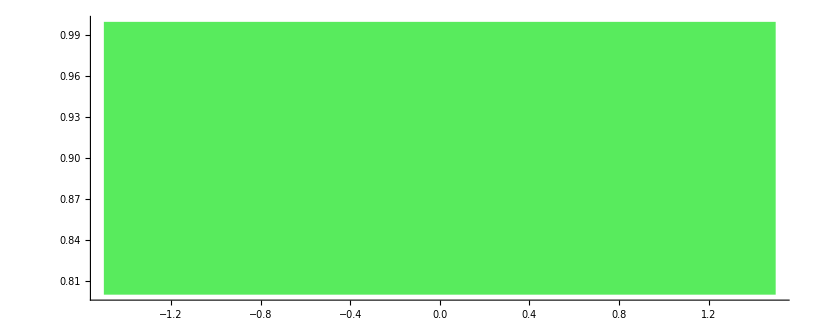

```mathematica
Graphics[{Opacity[0.8],Hue[0.34,0.8,0.9,0.8],Rectangle[{-1.5,1},{1.5,0.8}]},Axes->True]
```

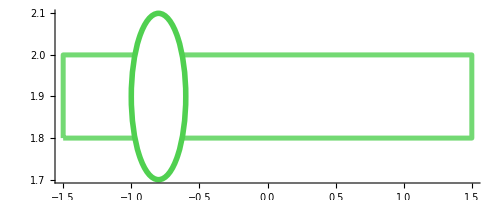

```mathematica
pr22=Show[{Graphics[{EdgeForm[Directive[Opacity[0.8],ColorData["Atoms"]["Ni"],Dashed,Thickness[0.009]]],White,Rectangle[{-1.5,1+1},{1.5,0.8+1}]},Axes->True],Graphics[{EdgeForm[Directive[Dashed,ColorData["Atoms"]["Ni"],Thickness[0.01]]],White,Disk[{-0.8,1.9},0.2]}]}]
```

```mathematica
Show[]
```

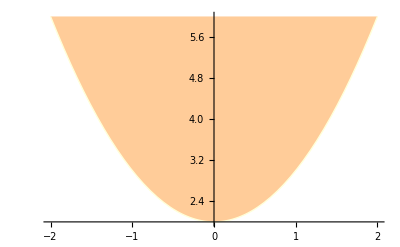

```mathematica
pt1=Plot[x^2+2,{x,-2,2},Axes->True,Filling->6,FillingStyle->Directive[Orange,Opacity[0.4]],PlotStyle->LightYellow]
```

```mathematica
ptlumo2=Graphics@Text[Style["LUMO",Bold,16],{1.9,1.9}];
```

```mathematica
par1=Graphics[{Dashed,Thickness[0.01],Arrowheads[0.07],Arrow[{{0,2},{0,1}}]}];
```

```mathematica
bal1=Graphics[{Dashed,ColorData["Atoms"]["Ni"],Thickness[0.01],Circle[{-0.8,2.0},0.4]}];
```

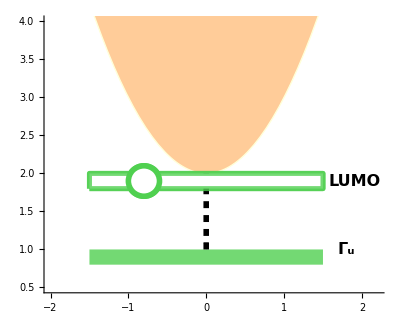

```mathematica
bgf1=Show[{pt1,pr2,pr22,ptlumo2,par1,pr22,glumo},PlotRange->{{-2.,2.2},{0.5,4}},AspectRatio->.8,Axes->True,AxesOrigin->{0,0}]
```

```mathematica
p1=Plot[x^2+2,{x,-2,2},Axes->True,Filling->6,FillingStyle->Directive[ColorData["Atoms"]["Th"],Opacity[0.7]],PlotStyle->LightYellow]
```

```mathematica
p2=Plot[-x^2-2,{x,-2,2},Axes->False,FillingStyle->Directive[ColorData["Atoms"]["Th"],Opacity[0.7]],Filling->-6,PlotStyle->LightPink]
```

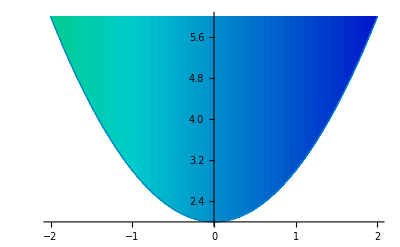

```mathematica
p1=Plot[x^2+2,{x,-2,2},Axes->True,Filling->6,ColorFunction->Function[{x,y},Hue[0.2x+0.45,1,.8]],PlotStyle->LightYellow]
```

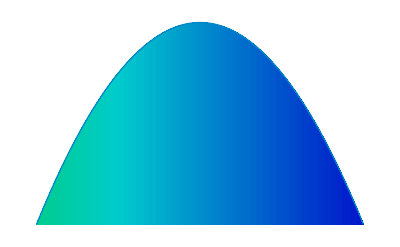

```mathematica
p2=Plot[-x^2-2,{x,-2,2},Axes->False,ColorFunction->Function[{x,y},Hue[0.2x+0.45,1,.8]],Filling->-6,PlotStyle->LightPink]
```

```mathematica
bal1=Graphics[{Dashed,Black,Opacity[0.8],Thickness[0.01],Disk[{-0.8,1.0-0.1},{0.2,0.2*(Sqrt@5+1)/2}]},ImageSize->100]
```

```mathematica
bal2=Graphics[{Dashed,Black,Opacity[0.8],Thickness[0.01],Disk[{-0.8,-1.0+0.1},{0.2,0.2*(Sqrt@5+1)/2}]},ImageSize->100];
```

```mathematica
bal3=Graphics[{Dashed,Black,Opacity[0.8],Thickness[0.01],Disk[{0.8,-1.0+0.1},{0.2,0.2*(Sqrt@5+1)/2}]},ImageSize->100];
```

```mathematica
Graphics[Polygon[{{0,-Sqrt[3]},{-1,0},{0,Sqrt[3]},{1,0}},VertexColors->{Red,Green,Blue}],ImageSize->50]
```

-Graphics-

### fo2

```mathematica
pthomo=Graphics@Text[Style["HOMO",Bold,16],{0,-2}];
ptlumo=Graphics@Text[Style["LUMO",Bold,16],{0,2}];
```

```mathematica
ghomo=Graphics@Text[Style["Γ_d",Bold,16],{1.8,-1}];
glumo=Graphics@Text[Style["Γ_u",Bold,16],{1.8,1}];
```

```mathematica
p1=Plot[x^2+2,{x,-2,2},Axes->True,Filling->6,ColorFunction->Function[{x,y},Hue[0.2x+0.45,1,.8]],PlotStyle->LightYellow]
```

```mathematica
p2=Plot[-x^2-2,{x,-2,2},Axes->False,ColorFunction->Function[{x,y},Hue[0.2x+0.45,1,.8]],Filling->-6,PlotStyle->LightPink]
```

new way to create a rectangle with fade color,,

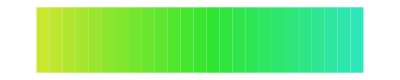

```mathematica
bar=Graphics[Table[{Hue[t/90+0.18,.8,.9,1],Rectangle[{ 1+t,1/10.}]},{t,25}],ImageSize->400]
```

```mathematica
Manipulate[Graphics[Table[{Hue[t/k,1,.9,.35],Disk[{Cos[2Pi t/15],Sin[2Pi t/15]}]},{t,15}],ImageSize->100],{k,1,20}]
```

```mathematica
elc=Graphics[Table[{Hue[t/15+0.01,1,.9,.2],Disk[{Cos[2Pi t/15],Sin[2Pi t/15]}]},{t,15}],ImageSize->100]
```

-Graphics-

```mathematica
elc=Graphics[Table[{Hue[t/1+0.01,1,.9,.2],Disk[{Cos[2Pi t/15],Sin[2Pi t/15]}]},{t,15}],ImageSize->100]
```

-Graphics-

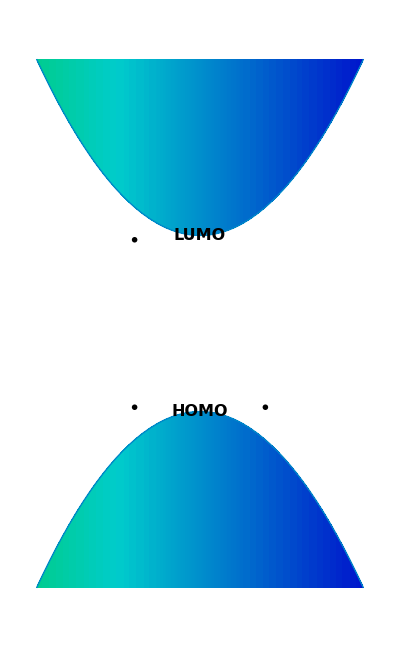

```mathematica
f1=Show[{p1,p2,pthomo,ptlumo},Epilog->{Inset[elc,{-0.8,2.0-0.1},Automatic,0.5],Inset[elc,{-0.8,-2.0+0.1},Automatic,0.5],Inset[elc,{0.8,-2.0+0.1},Automatic,0.5]},Prolog->{Inset[bar,{-0.,2.0-.1},Automatic,3.2],Inset[bar,{-0.,-2.0+0.1},Automatic,3.2]},PlotRange->All,AspectRatio->(Sqrt@5+1)/2,Axes->False,AxesOrigin->{0,0}]
```

```mathematica
Export["f2.png",f1,ImageResolution->600]
```

f2.png

```mathematica
SystemOpen["f1.png"]
```

```mathematica
pthomo2=Graphics@Text[Style["HOMO",Bold,16],{0,-1}];
ptlumo2=Graphics@Text[Style["LUMO",Bold,16],{0,1}];
```

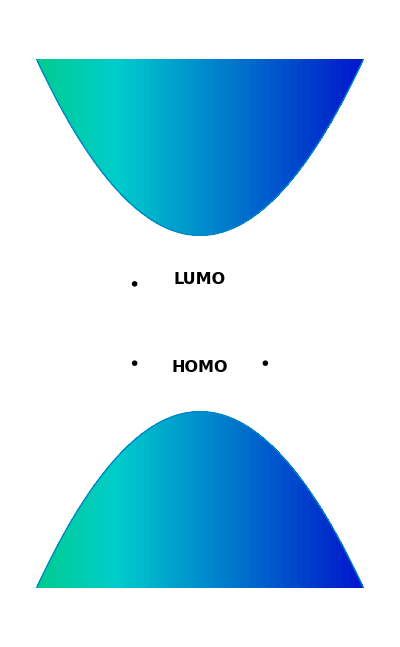

```mathematica
f2=Show[{p1,p2,pthomo2,ptlumo2},Epilog->{Inset[elc,{-0.8,1.0-0.1},Automatic,0.5],Inset[elc,{-0.8,-1.0+0.1},Automatic,0.5],Inset[elc,{0.8,-1.0+0.1},Automatic,0.5]},Prolog->{Inset[bar,{-0.,1.0-.1},Automatic,3.2],Inset[bar,{-0.,-1.0+0.1},Automatic,3.2]},PlotRange->All,AspectRatio->(Sqrt@5+1)/2,Axes->False,AxesOrigin->{0,0}]
```

```mathematica
f3=Show[{p1,p2,pthomo,ptlumo,ghomo,glumo},Epilog->{Inset[elc,{-0.8,1.0-0.1},Automatic,0.5],Inset[elc,{-0.8,-1.0+0.1},Automatic,0.5],Inset[elc,{0.8,-1.0+0.1},Automatic,0.5]},Prolog->{Inset[bar,{-0.,1.0-.1},Automatic,3.2],Inset[bar,{-0.,-1.0+0.1},Automatic,3.2]},PlotRange->All,AspectRatio->(Sqrt@5+1)/2,Axes->False,AxesOrigin->{0,0}]
```

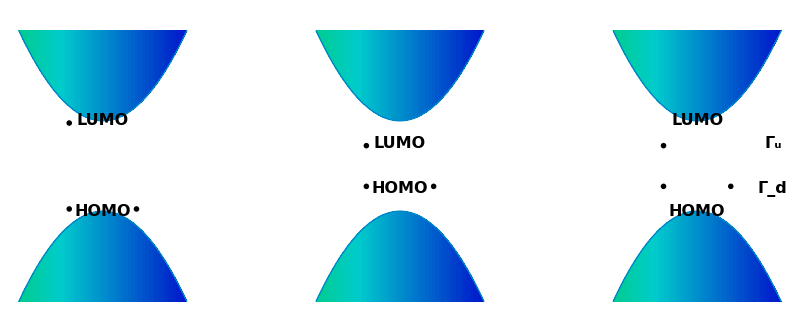

```mathematica
fo2=GraphicsRow[{f1,f2,f3},Epilog->{Inset[Graphics[{Thickness[.04],Gray,Dashed,Arrowheads[.2],Arrow[{{0,0},{1,0}}]}],{520,-300}],
Inset[Graphics[{Thickness[.04],Gray,Dashed,Arrowheads[.2],Arrow[{{0,0},{1,0}}]}],{1040,-300}],Inset[Style["DIMERIZATION",Bold,Gray,14],{510,-250}],Inset[Style["ORBITAL\nRENAME",Bold,Gray,14],{1030,-250}]},Spacings->160,Axes->False,ImageSize->800]
```

```mathematica
Export["fo2.png",fo2,ImageResolution->600]
```

fo2.png

This is it.

```mathematica
NotebookDirectory[]
```

C:\Users\John\SkyDrive\Documents\Task\NegPolaron\

## f2

### a

```mathematica
d2=Import["fig2.dat"];
```

```mathematica
Dimensions[d2]
```

```mathematica
f2=ListDensityPlot[d2[[1;;400]],PlotRange->All,ColorFunction->ColorData["AvocadoColors"],DataRange->{{0,200},{1,400}},ImageSize->380,FrameStyle->Directive[Thickness[0.006],FontSize->23,Bold],FrameLabel->{Style["Lattice Site",FontSize->23,Bold],Style["Time (fs)",FontSize->23,Bold]}]
```

```mathematica
Export["fig2.png",f2,ImageResolution->600]
```

```mathematica
SystemOpen["fig2.png"]
```

### b

```mathematica
d2c=Flatten@Import["fig2_c.dat"];
d2e=Flatten@Import["fig2_e.dat"];
```

```mathematica
f2c=ListPlot[{d2c,d2e},Joined->True,PlotRange->{{0,400},{-.1,1.2}},PlotStyle->{{ColorData["Atoms"]["Ba"],Thickness[.02]},{Orange,Thickness[.02]}},Axes->False,Frame->True,FrameStyle->Directive[Thickness[0.0062],FontSize->23,Bold],FrameLabel->{Style["Time (fs)",FontSize->23,Bold],Style["Electron Population",FontSize->23,Bold]},ImageSize->400,Epilog->{Inset[Style["Γ_u",Black,Bold,FontSize->16],{200.,.2}],Inset[Style["Γ_d",Black,Bold,FontSize->16],{200.,.8}]}]
```

```mathematica
Export["fig2_2.png",f2c,ImageResolution->600]
```

```mathematica
SystemOpen["fig2_2.png"]
```

## f3

```mathematica
d3=Import["fig3.dat"];
```

```mathematica
Dimensions[d3]
```

```mathematica
f3=ListDensityPlot[d3[[1;;400;;10]],PlotRange->All,ColorFunction->ColorData["AvocadoColors"],DataRange->{{0,200},{1,400}},ImageSize->380,FrameStyle->Directive[Thickness[0.006],FontSize->23,Bold],FrameLabel->{Style["Lattice Site",FontSize->23,Bold],Style["Time (fs)",FontSize->23,Bold]}]
```

```mathematica
Export["fig3.png",f3,ImageResolution->600]
```

```mathematica
SystemOpen["fig3.png"]
```

### b

```mathematica
d3c=Flatten@Import["fig3_c.dat"];
```

```mathematica
Dimensions[d3c]
```

```mathematica
f3c=ListPlot[{d3c,d3e},Joined->True,PlotRange->{{0,100},{-.1,1.2}},PlotStyle->{{ColorData["Atoms"]["Ba"],Opacity[.8],Thickness[.02]},{Orange,Opacity[.8],Thickness[.02]}},Axes->False,Frame->True,FrameStyle->Directive[Thickness[0.0062],FontSize->23,Bold],FrameLabel->{Style["Time (fs)",FontSize->23,Bold],Style["Electron Population",FontSize->23,Bold]},ImageSize->400,Epilog->{Inset[Style["Γ_u",Black,Bold,FontSize->16],{10.,.1}],Inset[Style["Γ_d",Black,Bold,FontSize->16],{10.,.9}]}]
```

```mathematica
Export["fig3_2.png",f3c,ImageResolution->600]
```

```mathematica
SystemOpen["fig3_2.png"]
```

### c

```mathematica
dcc=Import["figcc.dat"];
```

```mathematica
Dimensions[dcc]
```

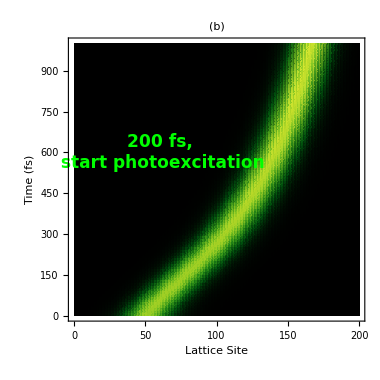

```mathematica
fcc=ListDensityPlot[dcc[[1;;100]],PlotRange->All,ColorFunction->ColorData["AvocadoColors"],DataRange->{{0,200},{1,1000}},ImageSize->380,FrameStyle->Directive[Thickness[0.006],FontSize->23,Bold],FrameLabel->{Style["Lattice Site",FontSize->23,Bold],Style["Time (fs)",FontSize->23,Bold]},Epilog->{Inset[Graphics[{Red,Thickness[.02],Opacity[.9],Arrowheads[.12],Arrow[{{0,1},{.0,0}}]}],{80,352}],Inset[Style["200 fs,\n start photoexcitation",Green,Bold,FontSize->17],{60,600}]},PlotLabel->Style["(b)",Bold,FontSize->23]]
```

```mathematica
Export["figcc2.png",fcc,ImageResolution->600]
```

## fig4

### a

```mathematica
d4=Import["fig4.dat"];
```

```mathematica
Dimensions[d4]
```

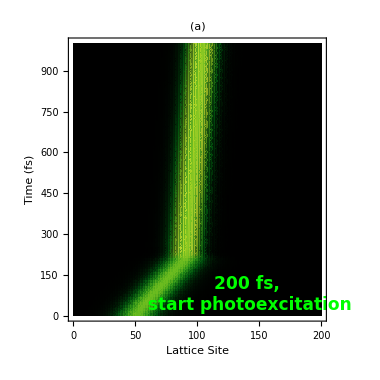

```mathematica
f4=ListDensityPlot[d4[[1;;1000;;10]],PlotRange->All,ColorFunction->ColorData["AvocadoColors"],DataRange->{{0,200},{1,1000}},ImageSize->380,FrameStyle->Directive[Thickness[0.006],FontSize->23,Bold],FrameLabel->{Style["Lattice Site",FontSize->23,Bold],Style["Time (fs)",FontSize->23,Bold]},Epilog->{Inset[Graphics[{Red,Thickness[.04],Opacity[.9],Arrowheads[.3],Arrow[{{.8,0},{0,0}}]}],{130,200}],Inset[Style["200 fs,\n start photoexcitation",Green,Bold,FontSize->17],{140,80}]},PlotLabel->Style["(a)",Bold,FontSize->23]]
```

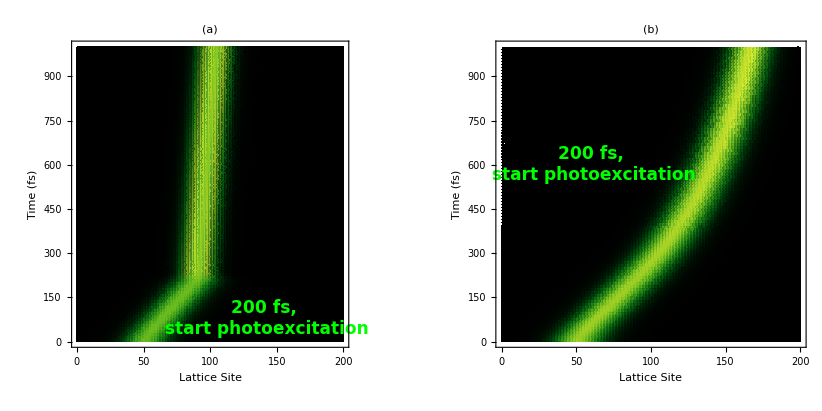

```mathematica
fc4=GraphicsRow[{f4,fcc}]
```

```mathematica
Export["fig4cc.png",fc4,ImageResolution->600]
```

fig4cc.png

```mathematica
SystemOpen["fig4.png"]
```

```mathematica
ColorData["AvocadoColors"]
```

### b

```mathematica
d4c=Flatten@Import["fig4_c.dat"];
d4e=Flatten@Import["fig4_e.dat"];
```

```mathematica
ListPlot[d4e,PlotRange->All]
```

```mathematica
ListPlot[d4c,PlotRange->All]
```

```mathematica
Dimensions[d4c]
```

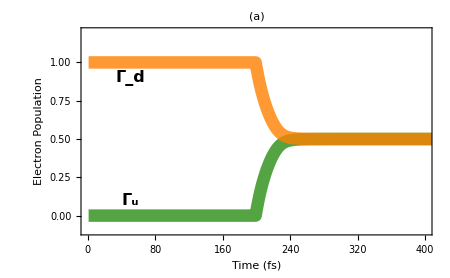

```mathematica
f4c=ListPlot[{d4c,d4e},Joined->True,PlotRange->{{0,400},{-.1,1.2}},PlotStyle->{{ColorData["Atoms"]["Ba"],Opacity[.8],Thickness[.02]},{Orange,Opacity[.8],Thickness[.02]}},Axes->False,Frame->True,FrameStyle->Directive[Thickness[0.0062],FontSize->23,Bold],FrameLabel->{Style["Time (fs)",FontSize->23,Bold],Style["Electron Population",FontSize->23,Bold]},ImageSize->450,Epilog->{Inset[Style["Γ_u",Black,Bold,FontSize->16],{50.,.1}],Inset[Style["Γ_d",Black,Bold,FontSize->16],{50.,.9}]},PlotLabel->Style["(a)",Bold,FontSize->23]]
```

```mathematica
Export["fig4_2.png",f4c,ImageResolution->600]
```

```mathematica
SystemOpen["fig4_2.png"]
```

### c

```mathematica
d4c=Flatten@Import["fig_cweak.dat"];
d4e=Flatten@Import["fig_eweak.dat"];
```

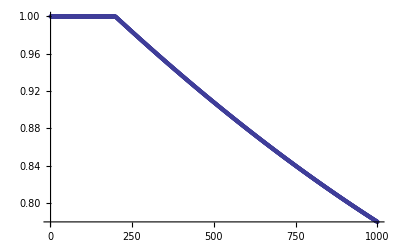

```mathematica
ListPlot[d4e,PlotRange->All]
```

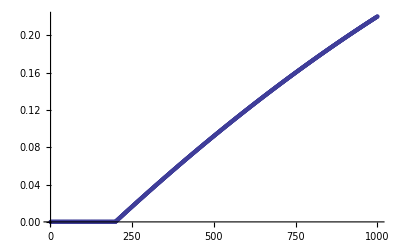

```mathematica
ListPlot[d4c,PlotRange->All]
```

```mathematica
Dimensions[d4c]
```

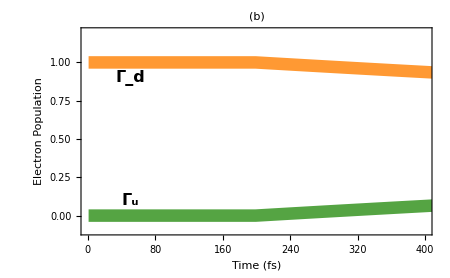

```mathematica
f4cc=ListPlot[{d4c,d4e},Joined->True,PlotRange->{{0,400},{-.1,1.2}},PlotStyle->{{ColorData["Atoms"]["Ba"],Opacity[.8],Thickness[.02]},{Orange,Opacity[.8],Thickness[.02]}},Axes->False,Frame->True,FrameStyle->Directive[Thickness[0.0062],FontSize->23,Bold],FrameLabel->{Style["Time (fs)",FontSize->23,Bold],Style["Electron Population",FontSize->23,Bold]},ImageSize->450,Epilog->{Inset[Style["Γ_u",Black,Bold,FontSize->16],{50.,.1}],Inset[Style["Γ_d",Black,Bold,FontSize->16],{50.,.9}]},PlotLabel->Style["(b)",Bold,FontSize->23]]
```

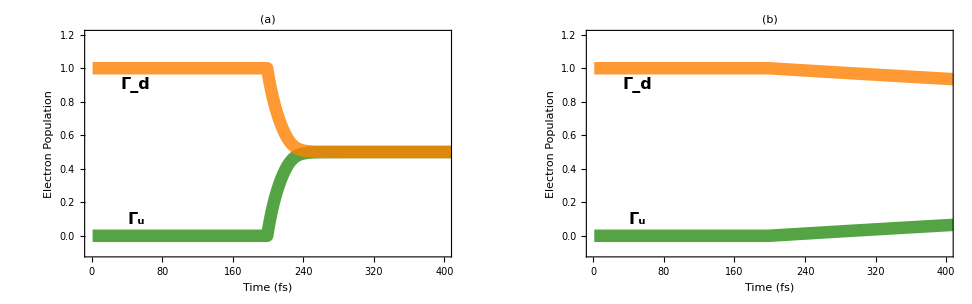

```mathematica
fe=GraphicsRow[{f4c,f4cc}]
```

```mathematica
Export["fig_e.png",fe,ImageResolution->600]
```

fig_e.png

```mathematica
SystemOpen["fig4_2.png"]
```

## c

### process

```mathematica
p1=Plot[x^2+2,{x,-2,2},Axes->False,Filling->6,FillingStyle->Directive[Orange,Opacity[0.4]],PlotStyle->LightYellow]
```

```mathematica
p2=Plot[-x^2-2,{x,-2,2},Axes->False,Filling->-6,FillingStyle->Directive[Red,Opacity[0.4]],PlotStyle->LightPink]
```

```mathematica
Show[p1,p2,PlotRange->All,AspectRatio->(Sqrt@5+1)/2]
```

```mathematica
pr1=Graphics[{Opacity[0.8],ColorData["Atoms"]["Pd"],Rectangle[{-1.5,-1},{1.5,-0.8}]}]
```

```mathematica
pr2=Graphics[{Opacity[0.8],ColorData["Atoms"]["Ni"],Rectangle[{-1.5,1},{1.5,0.8}]}]
```

```mathematica
{λ,sx,sy,x0,y0,len}={1./4.,3,0.2,-1.5,-1,0.9*8*sy};
pa1=Graphics[{Opacity[0.8],Black,Thickness[0.02],Arrowheads[.078],Arrow[{{λ*sx+x0,y0+sy/2.-len/2.},{λ*sx+x0,y0+sy/2.+len/2.}}]}];
{λ,sx,sy,x1,y1,len}={1./4.,3,0.2,-1.5,1,0.6*8*sy};
pa2=Graphics[{Opacity[0.8],Black,Thickness[0.02],Arrowheads[.078],Arrow[{{λ*sx+x1,y1+sy/2.-len/2.},{λ*sx+x1,y1+sy/2.+len/2.}}]}];
```

```mathematica
ip1=0.2;
ip2=1.2;
pa3=Graphics[{Opacity[0.6],Black,Dashed,Thickness[0.01],Arrowheads[Large],Arrow[BezierCurve[{{λ*sx+x0+ip1,y0+sy/2.},{λ*sx+x0+ip2,(y0+y1)/2.},{λ*sx+x1+ip1,y1+sy/2.}}]]}]
```

```mathematica
pthomo=Graphics@Text[Style["HOMO",Bold,16],{0,-2}];
ptlumo=Graphics@Text[Style["LUMO",Bold,16],{0,2}];
```

```mathematica
rm=0.2;
pttext=Graphics[{Opacity[.8],Text[Style["Move Up",Bold,16],{λ*sx+x0+ip2+rm,(y0+y1)/2.}]}];
```

```mathematica
ghomo=Graphics@Text[Style["Γ_d",Bold,16],{1.8,-1}];
glumo=Graphics@Text[Style["Γ_u",Bold,16],{1.8,1}];
```

```mathematica
f4d=Show[{p1,p2,pr1,pr2,pa1,pa2,pa3,pthomo,ptlumo,ghomo,glumo,pttext},PlotRange->All,AspectRatio->(Sqrt@5+1)/2,Axes->False,AxesOrigin->{0,0}]
```

### end

```mathematica
p1=Plot[x^2+2,{x,-2,2},Axes->False,Filling->6,FillingStyle->Directive[Orange,Opacity[0.4]],PlotStyle->LightYellow]
```

```mathematica
p2=Plot[-x^2-2,{x,-2,2},Axes->False,Filling->-6,FillingStyle->Directive[Red,Opacity[0.4]],PlotStyle->LightPink]
```

```mathematica
Show[p1,p2,PlotRange->All,AspectRatio->(Sqrt@5+1)/2]
```

```mathematica
pr1=Graphics[{Opacity[0.8],ColorData["Atoms"]["Pd"],Rectangle[{-1.5,-1},{1.5,-0.8}]}]
```

```mathematica
pr2=Graphics[{Opacity[0.8],ColorData["Atoms"]["Ni"],Rectangle[{-1.5,1},{1.5,0.8}]}]
```

```mathematica
{λ,sx,sy,x0,y0,len}={1./4.,3,0.2,-1.5,-1,0.6*8*sy};
pa1=Graphics[{Opacity[0.8],Black,Thickness[0.02],Arrowheads[.078],Arrow[{{λ*sx+x0,y0+sy/2.-len/2.},{λ*sx+x0,y0+sy/2.+len/2.}}]}];
{λ,sx,sy,x1,y1,len}={1./4.,3,0.2,-1.5,1,0.6*8*sy};
pa2=Graphics[{Opacity[0.8],Black,Thickness[0.02],Arrowheads[.078],Arrow[{{λ*sx+x1,y1+sy/2.-len/2.},{λ*sx+x1,y1+sy/2.+len/2.}}]}];
```

```mathematica
ip1=0.2;
ip2=1.2;
```

```mathematica
pthomo=Graphics@Text[Style["HOMO",Bold,16],{0,-2}];
ptlumo=Graphics@Text[Style["LUMO",Bold,16],{0,2}];
```

```mathematica
ghomo=Graphics@Text[Style["Γ_d",Bold,16],{1.8,-1}];
glumo=Graphics@Text[Style["Γ_u",Bold,16],{1.8,1}];
```

```mathematica
f5d=Show[{p1,p2,pr1,pr2,pa1,pa2,pthomo,ptlumo,ghomo,glumo},PlotRange->All,AspectRatio->(Sqrt@5+1)/2,Axes->False,AxesOrigin->{0,0}]
```

```mathematica
fc=GraphicsRow[{f1,f4d,f5d},Epilog->{Inset[Graphics[{Thickness[.04],Gray,Dashed,Arrowheads[.2],Arrow[{{0,0},{1,0}}]}],{520,-300}],
Inset[Graphics[{Thickness[.04],Gray,Dashed,Arrowheads[.2],Arrow[{{0,0},{1,0}}]}],{1040,-300}]},Spacings->160,Axes->False,ImageSize->800]
```

```mathematica
Export["f4_3.png",fc,ImageResolution->600]
```

```mathematica
SystemOpen["f4_3.png"]
```

## Configuration

```mathematica
config=Import["config.dat"];
```

```mathematica
Dimensions@config
```

```mathematica
Graphics[#1,ImageSize->20]&/@Array[{Hue[#1],Disk[]}&,20,{0.,1.}]
```

```mathematica
p[1]=ListPlot3D[config[[1;;80,All]],PlotRange->All,DataRange->{{0,200},{1,800}},Mesh->Automatic,ColorFunctionScaling->True,PlotStyle->{White,Specularity[White,10]},Lighting->{{"Directional",Hue[0.12],{{-200,-800,-.4},{-5,-5,0}}}}]
```

```mathematica
ColorData["Gradients"]
```

```mathematica
p[1]=ListPlot3D[config[[1;;80,All]],PlotRange->All,DataRange->{{0,200},{1,800}},Mesh->10,ColorFunctionScaling->True,Lighting->Automatic,PlotStyle->Opacity[0.8],ColorFunction->Function[{x,y,z},ColorData[{"Rainbow","Reverse"}][Rescale[z,{0,0.9}]]]]
```

```mathematica
renderp[1]=Show[p[1],BoxStyle->Directive[{Bold,FontSize->20,Thickness[0.006]}],ImageSize->450,Axes-> True,LabelStyle->Directive[Bold,20],PlotLabel->Style[" ",Bold,20],AspectRatio->1/1.218,Ticks->{Automatic,Array[#1&,5,{0,1000}],Automatic},ViewPoint->{-2.11899347072187,2.1819542421422633,-1.4828831229181403},ViewVertical->{0,0,-1},AxesLabel->{Nest[StringJoin[" ",#1]&,"Lattice Site",10],Nest[StringJoin[" ",#1]&,"Times (fs)   ",0],""}]
```

```mathematica
Export["config.png",renderp[1],ImageResolution->500]
```

```mathematica
SystemOpen["config.png"]
```

```mathematica
f1=ListPlot[config[[1]],PlotRange->All,Axes->False,Frame->True,AspectRatio->0.8,PlotStyle->Directive[Red,Thickness[0.012]],FrameStyle->Directive[Black,FontSize->23,Bold],Joined->True,FrameLabel->{Style["Lattice Site",FontSize->23,Bold],Style["Lattice Configuration",FontSize->23,Bold]},ImageSize->400]
```

```mathematica
f2=ListPlot[config[[100]],PlotRange->All,Axes->False,Frame->True,AspectRatio->0.8,PlotStyle->{Directive[Blue,Thickness[0.012]],Opacity[0.6]},FrameStyle->Directive[Black,FontSize->23,Bold],Joined->True,FrameLabel->{Style["Lattice Site",FontSize->23,Bold],Style["Lattice Configuration",FontSize->23,Bold]},ImageSize->400]
```

```mathematica
Show[{f1,f2}]
```